```mathematica
(* set up the Levy alpha-stable SDE *)
α=1;
(* drift *)
(* f[x_] := Sin[x] *)
f[x_]:=-10 x*Exp[-2x^2];
(* constant diffusion *)
g=0.25;
```

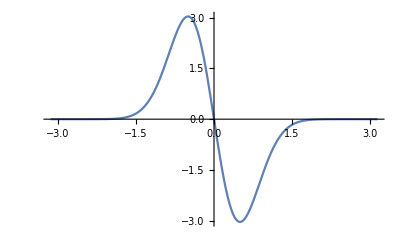

```mathematica
Plot[f[x],{x,-π,π}]
```

```mathematica
ntraj=500;
nsamp=1;
plots=Table[{},{i,ntraj}];
tvec=Table[j*dt,{j,0,numsteps}];
dt = 0.001;
numsteps=400;
ns = numsteps;
For[traj=1,traj≤ntraj,traj+=1,
mcsol=Table[0,ns+1];
mcsol[[1]]=0.0; (* initial condition *)
For[i=1,i≤ns,i+=1,
mcsol[[i+1]] =mcsol[[i]]+ (dt*f[mcsol[[i]]] +  RandomVariate[StableDistribution[1,α,0.0,0.0,dt g],nsamp]);
];
fname=StringJoin["mcsolgauss",ToString[traj],".csv"];
Print[fname];
Export[fname,mcsol];
plots[[traj]]=ListPlot[Transpose[{tvec,Flatten[mcsol]}]]
]
```

mcsolgauss1.csv

mcsolgauss2.csv

mcsolgauss3.csv

mcsolgauss4.csv

mcsolgauss5.csv

mcsolgauss6.csv

mcsolgauss7.csv

mcsolgauss8.csv

mcsolgauss9.csv

mcsolgauss10.csv

mcsolgauss11.csv

mcsolgauss12.csv

mcsolgauss13.csv

mcsolgauss14.csv

mcsolgauss15.csv

mcsolgauss16.csv

mcsolgauss17.csv

mcsolgauss18.csv

mcsolgauss19.csv

mcsolgauss20.csv

mcsolgauss21.csv

mcsolgauss22.csv

mcsolgauss23.csv

mcsolgauss24.csv

mcsolgauss25.csv

mcsolgauss26.csv

mcsolgauss27.csv

mcsolgauss28.csv

mcsolgauss29.csv

mcsolgauss30.csv

mcsolgauss31.csv

mcsolgauss32.csv

mcsolgauss33.csv

mcsolgauss34.csv

mcsolgauss35.csv

mcsolgauss36.csv

mcsolgauss37.csv

mcsolgauss38.csv

mcsolgauss39.csv

mcsolgauss40.csv

mcsolgauss41.csv

mcsolgauss42.csv

mcsolgauss43.csv

mcsolgauss44.csv

mcsolgauss45.csv

mcsolgauss46.csv

mcsolgauss47.csv

mcsolgauss48.csv

mcsolgauss49.csv

mcsolgauss50.csv

mcsolgauss51.csv

mcsolgauss52.csv

mcsolgauss53.csv

mcsolgauss54.csv

mcsolgauss55.csv

mcsolgauss56.csv

mcsolgauss57.csv

mcsolgauss58.csv

mcsolgauss59.csv

mcsolgauss60.csv

mcsolgauss61.csv

mcsolgauss62.csv

mcsolgauss63.csv

mcsolgauss64.csv

mcsolgauss65.csv

mcsolgauss66.csv

mcsolgauss67.csv

mcsolgauss68.csv

mcsolgauss69.csv

mcsolgauss70.csv

mcsolgauss71.csv

mcsolgauss72.csv

mcsolgauss73.csv

mcsolgauss74.csv

mcsolgauss75.csv

mcsolgauss76.csv

mcsolgauss77.csv

mcsolgauss78.csv

mcsolgauss79.csv

mcsolgauss80.csv

mcsolgauss81.csv

mcsolgauss82.csv

mcsolgauss83.csv

mcsolgauss84.csv

mcsolgauss85.csv

mcsolgauss86.csv

mcsolgauss87.csv

mcsolgauss88.csv

mcsolgauss89.csv

mcsolgauss90.csv

mcsolgauss91.csv

mcsolgauss92.csv

mcsolgauss93.csv

mcsolgauss94.csv

mcsolgauss95.csv

mcsolgauss96.csv

mcsolgauss97.csv

mcsolgauss98.csv

mcsolgauss99.csv

mcsolgauss100.csv

mcsolgauss101.csv

mcsolgauss102.csv

mcsolgauss103.csv

mcsolgauss104.csv

mcsolgauss105.csv

mcsolgauss106.csv

mcsolgauss107.csv

mcsolgauss108.csv

mcsolgauss109.csv

mcsolgauss110.csv

mcsolgauss111.csv

mcsolgauss112.csv

mcsolgauss113.csv

mcsolgauss114.csv

mcsolgauss115.csv

mcsolgauss116.csv

mcsolgauss117.csv

mcsolgauss118.csv

mcsolgauss119.csv

mcsolgauss120.csv

mcsolgauss121.csv

mcsolgauss122.csv

mcsolgauss123.csv

mcsolgauss124.csv

mcsolgauss125.csv

mcsolgauss126.csv

mcsolgauss127.csv

mcsolgauss128.csv

mcsolgauss129.csv

mcsolgauss130.csv

mcsolgauss131.csv

mcsolgauss132.csv

mcsolgauss133.csv

mcsolgauss134.csv

mcsolgauss135.csv

mcsolgauss136.csv

mcsolgauss137.csv

mcsolgauss138.csv

mcsolgauss139.csv

mcsolgauss140.csv

mcsolgauss141.csv

mcsolgauss142.csv

mcsolgauss143.csv

mcsolgauss144.csv

mcsolgauss145.csv

mcsolgauss146.csv

mcsolgauss147.csv

mcsolgauss148.csv

mcsolgauss149.csv

mcsolgauss150.csv

mcsolgauss151.csv

mcsolgauss152.csv

mcsolgauss153.csv

mcsolgauss154.csv

mcsolgauss155.csv

mcsolgauss156.csv

mcsolgauss157.csv

mcsolgauss158.csv

mcsolgauss159.csv

mcsolgauss160.csv

mcsolgauss161.csv

mcsolgauss162.csv

mcsolgauss163.csv

mcsolgauss164.csv

mcsolgauss165.csv

mcsolgauss166.csv

mcsolgauss167.csv

mcsolgauss168.csv

mcsolgauss169.csv

mcsolgauss170.csv

mcsolgauss171.csv

mcsolgauss172.csv

mcsolgauss173.csv

mcsolgauss174.csv

mcsolgauss175.csv

mcsolgauss176.csv

mcsolgauss177.csv

mcsolgauss178.csv

mcsolgauss179.csv

mcsolgauss180.csv

mcsolgauss181.csv

mcsolgauss182.csv

mcsolgauss183.csv

mcsolgauss184.csv

mcsolgauss185.csv

mcsolgauss186.csv

mcsolgauss187.csv

mcsolgauss188.csv

mcsolgauss189.csv

mcsolgauss190.csv

mcsolgauss191.csv

mcsolgauss192.csv

mcsolgauss193.csv

mcsolgauss194.csv

mcsolgauss195.csv

mcsolgauss196.csv

mcsolgauss197.csv

mcsolgauss198.csv

mcsolgauss199.csv

mcsolgauss200.csv

mcsolgauss201.csv

mcsolgauss202.csv

mcsolgauss203.csv

mcsolgauss204.csv

mcsolgauss205.csv

mcsolgauss206.csv

mcsolgauss207.csv

mcsolgauss208.csv

mcsolgauss209.csv

mcsolgauss210.csv

mcsolgauss211.csv

mcsolgauss212.csv

mcsolgauss213.csv

mcsolgauss214.csv

mcsolgauss215.csv

mcsolgauss216.csv

mcsolgauss217.csv

mcsolgauss218.csv

mcsolgauss219.csv

mcsolgauss220.csv

mcsolgauss221.csv

mcsolgauss222.csv

mcsolgauss223.csv

mcsolgauss224.csv

mcsolgauss225.csv

mcsolgauss226.csv

mcsolgauss227.csv

mcsolgauss228.csv

mcsolgauss229.csv

mcsolgauss230.csv

mcsolgauss231.csv

mcsolgauss232.csv

mcsolgauss233.csv

mcsolgauss234.csv

mcsolgauss235.csv

mcsolgauss236.csv

mcsolgauss237.csv

mcsolgauss238.csv

mcsolgauss239.csv

mcsolgauss240.csv

mcsolgauss241.csv

mcsolgauss242.csv

mcsolgauss243.csv

mcsolgauss244.csv

mcsolgauss245.csv

mcsolgauss246.csv

mcsolgauss247.csv

mcsolgauss248.csv

mcsolgauss249.csv

mcsolgauss250.csv

mcsolgauss251.csv

mcsolgauss252.csv

mcsolgauss253.csv

mcsolgauss254.csv

mcsolgauss255.csv

mcsolgauss256.csv

mcsolgauss257.csv

mcsolgauss258.csv

mcsolgauss259.csv

mcsolgauss260.csv

mcsolgauss261.csv

mcsolgauss262.csv

mcsolgauss263.csv

mcsolgauss264.csv

mcsolgauss265.csv

mcsolgauss266.csv

mcsolgauss267.csv

mcsolgauss268.csv

mcsolgauss269.csv

mcsolgauss270.csv

mcsolgauss271.csv

mcsolgauss272.csv

mcsolgauss273.csv

mcsolgauss274.csv

mcsolgauss275.csv

mcsolgauss276.csv

mcsolgauss277.csv

mcsolgauss278.csv

mcsolgauss279.csv

mcsolgauss280.csv

mcsolgauss281.csv

mcsolgauss282.csv

mcsolgauss283.csv

mcsolgauss284.csv

mcsolgauss285.csv

mcsolgauss286.csv

mcsolgauss287.csv

mcsolgauss288.csv

mcsolgauss289.csv

mcsolgauss290.csv

mcsolgauss291.csv

mcsolgauss292.csv

mcsolgauss293.csv

mcsolgauss294.csv

mcsolgauss295.csv

mcsolgauss296.csv

mcsolgauss297.csv

mcsolgauss298.csv

mcsolgauss299.csv

mcsolgauss300.csv

mcsolgauss301.csv

mcsolgauss302.csv

mcsolgauss303.csv

mcsolgauss304.csv

mcsolgauss305.csv

mcsolgauss306.csv

mcsolgauss307.csv

mcsolgauss308.csv

mcsolgauss309.csv

mcsolgauss310.csv

mcsolgauss311.csv

mcsolgauss312.csv

mcsolgauss313.csv

mcsolgauss314.csv

mcsolgauss315.csv

mcsolgauss316.csv

mcsolgauss317.csv

mcsolgauss318.csv

mcsolgauss319.csv

mcsolgauss320.csv

mcsolgauss321.csv

mcsolgauss322.csv

mcsolgauss323.csv

mcsolgauss324.csv

mcsolgauss325.csv

mcsolgauss326.csv

mcsolgauss327.csv

mcsolgauss328.csv

mcsolgauss329.csv

mcsolgauss330.csv

mcsolgauss331.csv

mcsolgauss332.csv

mcsolgauss333.csv

mcsolgauss334.csv

mcsolgauss335.csv

mcsolgauss336.csv

mcsolgauss337.csv

mcsolgauss338.csv

mcsolgauss339.csv

mcsolgauss340.csv

mcsolgauss341.csv

mcsolgauss342.csv

mcsolgauss343.csv

mcsolgauss344.csv

mcsolgauss345.csv

mcsolgauss346.csv

mcsolgauss347.csv

mcsolgauss348.csv

mcsolgauss349.csv

mcsolgauss350.csv

mcsolgauss351.csv

mcsolgauss352.csv

mcsolgauss353.csv

mcsolgauss354.csv

mcsolgauss355.csv

mcsolgauss356.csv

mcsolgauss357.csv

mcsolgauss358.csv

mcsolgauss359.csv

mcsolgauss360.csv

mcsolgauss361.csv

mcsolgauss362.csv

mcsolgauss363.csv

mcsolgauss364.csv

mcsolgauss365.csv

mcsolgauss366.csv

mcsolgauss367.csv

mcsolgauss368.csv

mcsolgauss369.csv

mcsolgauss370.csv

mcsolgauss371.csv

mcsolgauss372.csv

mcsolgauss373.csv

mcsolgauss374.csv

mcsolgauss375.csv

mcsolgauss376.csv

mcsolgauss377.csv

mcsolgauss378.csv

mcsolgauss379.csv

mcsolgauss380.csv

mcsolgauss381.csv

mcsolgauss382.csv

mcsolgauss383.csv

mcsolgauss384.csv

mcsolgauss385.csv

mcsolgauss386.csv

mcsolgauss387.csv

mcsolgauss388.csv

mcsolgauss389.csv

mcsolgauss390.csv

mcsolgauss391.csv

mcsolgauss392.csv

mcsolgauss393.csv

mcsolgauss394.csv

mcsolgauss395.csv

mcsolgauss396.csv

mcsolgauss397.csv

mcsolgauss398.csv

mcsolgauss399.csv

mcsolgauss400.csv

mcsolgauss401.csv

mcsolgauss402.csv

mcsolgauss403.csv

mcsolgauss404.csv

mcsolgauss405.csv

mcsolgauss406.csv

mcsolgauss407.csv

mcsolgauss408.csv

mcsolgauss409.csv

mcsolgauss410.csv

mcsolgauss411.csv

mcsolgauss412.csv

mcsolgauss413.csv

mcsolgauss414.csv

mcsolgauss415.csv

mcsolgauss416.csv

mcsolgauss417.csv

mcsolgauss418.csv

mcsolgauss419.csv

mcsolgauss420.csv

mcsolgauss421.csv

mcsolgauss422.csv

mcsolgauss423.csv

mcsolgauss424.csv

mcsolgauss425.csv

mcsolgauss426.csv

mcsolgauss427.csv

mcsolgauss428.csv

mcsolgauss429.csv

mcsolgauss430.csv

mcsolgauss431.csv

mcsolgauss432.csv

mcsolgauss433.csv

mcsolgauss434.csv

mcsolgauss435.csv

mcsolgauss436.csv

mcsolgauss437.csv

mcsolgauss438.csv

mcsolgauss439.csv

mcsolgauss440.csv

mcsolgauss441.csv

mcsolgauss442.csv

mcsolgauss443.csv

mcsolgauss444.csv

mcsolgauss445.csv

mcsolgauss446.csv

mcsolgauss447.csv

mcsolgauss448.csv

mcsolgauss449.csv

mcsolgauss450.csv

mcsolgauss451.csv

mcsolgauss452.csv

mcsolgauss453.csv

mcsolgauss454.csv

mcsolgauss455.csv

mcsolgauss456.csv

mcsolgauss457.csv

mcsolgauss458.csv

mcsolgauss459.csv

mcsolgauss460.csv

mcsolgauss461.csv

mcsolgauss462.csv

mcsolgauss463.csv

mcsolgauss464.csv

mcsolgauss465.csv

mcsolgauss466.csv

mcsolgauss467.csv

mcsolgauss468.csv

mcsolgauss469.csv

mcsolgauss470.csv

mcsolgauss471.csv

mcsolgauss472.csv

mcsolgauss473.csv

mcsolgauss474.csv

mcsolgauss475.csv

mcsolgauss476.csv

mcsolgauss477.csv

mcsolgauss478.csv

mcsolgauss479.csv

mcsolgauss480.csv

mcsolgauss481.csv

mcsolgauss482.csv

mcsolgauss483.csv

mcsolgauss484.csv

mcsolgauss485.csv

mcsolgauss486.csv

mcsolgauss487.csv

mcsolgauss488.csv

mcsolgauss489.csv

mcsolgauss490.csv

mcsolgauss491.csv

mcsolgauss492.csv

mcsolgauss493.csv

mcsolgauss494.csv

mcsolgauss495.csv

mcsolgauss496.csv

mcsolgauss497.csv

mcsolgauss498.csv

mcsolgauss499.csv

mcsolgauss500.csv

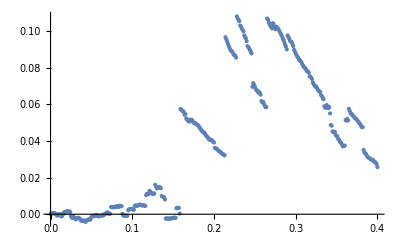
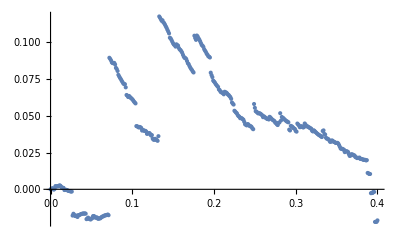
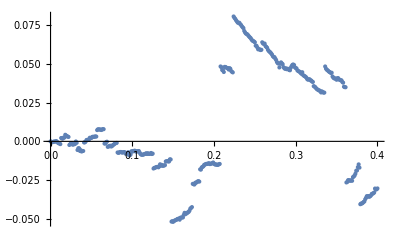
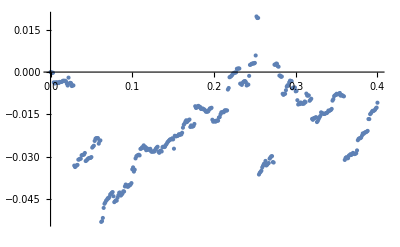
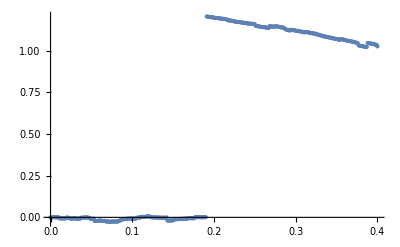
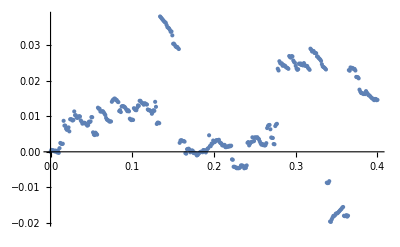
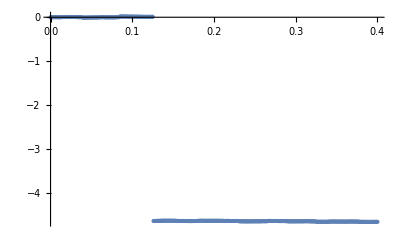
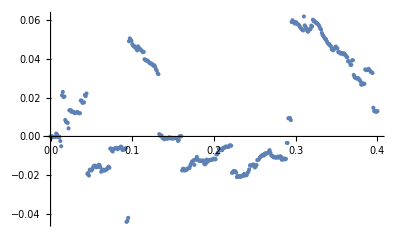
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
plots
```

```mathematica
ListPlot[Transpose[{tvec,Flatten[mcsol]}]]
```

-Graphics-

```mathematica
Export["mcsolgauss.csv",mcsol]
```

mcsolgauss.csv

```mathematica
StringJoin["mcsolgauss",ToString[2],".csv"]
```

mcsolgauss2.csv